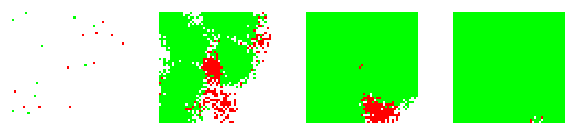

```mathematica
name="2species-env-circle-1";
SetDirectory[NotebookDirectory[]];
<<"DisplayLibrary.wl";
data =Get[name<>".dat"];
mPlotPlants[data]
g=mPlantGrid[data,{1,4,7,10}]
Export[name<>".png",g];
```